```mathematica
(* Initialize Mathematica *)
Clear["`*"];
SetDirectory["GitHub/MaxPol"];
$HistoryLength=0;

maxpol[n_,l_,P_]:=Module[{Q,a,V,VaP,VaQ,L,cs,b,lhs},
On[Assert];
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
Assert[0^0==1];

(* Check parameters *)
Q=2l-1-P;
a=-l-1; (* s=0 zero shift central scheme *)
Assert[2l>=P&&P>=n];

(* Generate Matrices *)
V[a_,J_]:=Table[(a+x)^y,{y,0,J},{x,1,2l+1}];
VaP=V[a,P];
VaQ=V[a,Q];
L=DiagonalMatrix[Table[(-1)^k,{k,1,2l+1}]];
cs=Table[Subscript[c, k],{k,1,2l+1}];
b=SparseArray[{n+1}->Factorial[n],2l+1];
lhs=If[Q>=0,ArrayFlatten[{{VaP},{VaQ.L}}],VaP];

(* Solve System *)
cs/.Solve[lhs.cs==b,cs][[1]]//Simplify
]
```

```mathematica
(* Careful: Slow calculation! I experienced a memory leak during execution, so you're advised to split the execution into separate parts. *)
save[n_,l_,P_]:=Module[{r},
r=maxpol[n,l,P];
Export[StringForm["maxpol_calc/maxpol_n``_l``_P``",n,l,P]//ToString,N[r,18],"csv"];
Export[StringForm["maxpol_calc_exact/maxpol_exact_n``_l``_P``",n,l,P]//ToString,r,"csv"];
];
Monitor[Do[Do[Do[save[n,l,P] ,{P,n,2l}],{l,1,100}],{n,0,4}],{n,l,P}]
```

```mathematica
(* Import solution *)
demo[n_,l_,factor_]:=Module[{P,solution,H},
P=Round[n+(2l-n)(1-factor)]; (* degree of lowpass. (lowpass) n <= P <= 2l (fullband) *)
solution=Import[StringForm["maxpol_calc/maxpol_n``_l``_P``",n,l,P]//ToString,"csv"]//Flatten;

(* Convolution shape *)
ListPlot[solution,PlotMarkers->Automatic,PlotRange->Full,Ticks->{None,Automatic}, Filling->Axis,FillingStyle->Thickness[0.005]];
(* Spectrum *)
H[w_]:=Abs[Sum[solution[[k]]Exp[ⅈ k w],{k,1,2l+1}]];
Plot[{w^n,H[w]},{w,0,Pi},PlotRange->{Full,{10^-12,Automatic}},PlotLegends->{"Exact Derivative","MaxPol"},AxesLabel->{"ω","|H|"}, Ticks->{Table[i Pi,{i,0,1,1/4}],Automatic}]
];
Manipulate[demo[n,l,factor],{n,0,4,1},{factor,0,1},{l,1,100,1}]
```

```mathematica
findCutoff[n_,l_,P_]:=Module[{solution,max,H},
solution=Import[StringForm["maxpol_calc/maxpol_n``_l``_P``",n,l,P]//ToString,"csv"]//Flatten;
H[w_]:=Abs[Sum[solution[[k]]Exp[ⅈ k w],{k,1,2l+1}]];
max=FindMaximum[H[f Pi],{f,P/(2l),0,1}];
Assert[max[[1]]>10^-5];(* Sanity check *)
Return[f/.max[[2]]];
];
findCutoff[1,50,25]
```

```mathematica
saveCutoff[n_,l_,P_]:=Module[{r},
r=findCutoff[n,l,P];
Export[StringForm["maxpol_calc_cutoff/maxpol_cutoff_n``_l``_P``",n,l,P]//ToString,N[r,18],"csv"];
];
Monitor[Do[Do[Do[saveCutoff[n,l,P] ,{P,n,2l}],{l,1,100}],{n,1,4}],{n,l,P}]
```

FittedModel[0.116687+0.693085 x]

0.995067

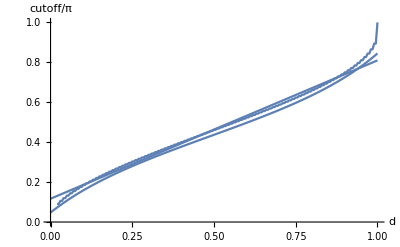

```mathematica
demoCutoff[n_,l_]:=Module[{solution,fit,amt,ignore},
solution=Table[{P/(2l),Import[StringForm["maxpol_calc_cutoff/maxpol_cutoff_n``_l``_P``",n,l,P]//ToString,"csv"][[1]][[1]]},{P,n,2l}];
amt=Length[solution];
ignore=5;
(*fit=NonlinearModelFit[solution[[ignore;;amt-ignore]],a Tan[b x-c]+d,{a,b,{c,0.5},{d,0.5}},x];*)
fit=LinearModelFit[solution[[ignore;;amt-ignore]],x,x];
Print[fit];
Print[fit["RSquared"]];
Show[
ListPlot[solution,PlotRange->Full,Joined->True,AxesLabel->{"d","cutoff/π"}],
Plot[fit[d],{d,0,1}],
Plot[0.43-0.35Tan[0.83-1.7d],{d,0,1}]
]
];
demoCutoff[4,100]
```